# Complex Data fitting in Mathematica

A short notebook that show how to fit data in Mathematica

### Example Function

Microwave resonators are always good proxy. Using:
ω0 resonance
κ radiative decay 
γ non radiative decay
ω probing angular frequency

```mathematica
S11=((ω-ω0)^2+(κ^2-γ^2)+2 ⅈ γ (ω-ω0))/((ω-ω0)^2+(κ+γ)^2);
```

### Plot the function

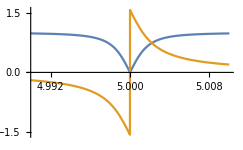

```mathematica
myω0=2π 5.0;
myκ=2π 0.001;
myγ=2π 0.001;
myParam={κ->myκ, γ->myγ, ω0->myω0};
Plot[{Abs@S11/.myParam/.ω->2π x,Arg@S11/.myParam/.ω->2π x},{x,4.99,5.01}, PlotRange->All]
```

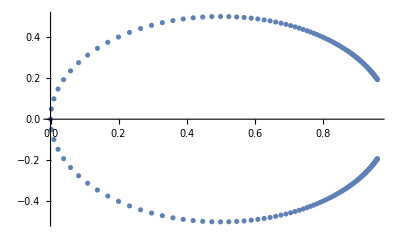

```mathematica
ListPlot[Table[{Re@S11/.myParam/.ω->2π x,Im@S11/.myParam/.ω->2π x},{x,4.99,5.01,0.0001}]]
```

### Generating Noise data to fit

Generate some some data (both complex and real to fit)

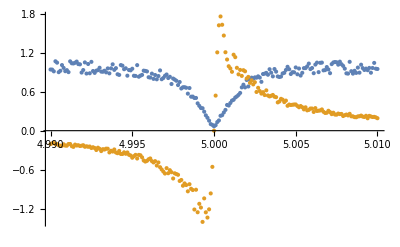

```mathematica
fitDataComplex=Table[{x, Random[Complex,{-0.1,0.1}]+S11/.myParam/.ω->2π x},{x,4.99,5.01,0.0001}];
fitDataMagnitude=Table[{x, Abs[(Random[Complex,{-0.1,0.1}]+S11/.myParam/.ω->2π x)]},{x,4.99,5.01,0.0001}];
fitDataPhase=Table[{x, Arg[(Random[Complex,{-0.1,0.1}]+S11/.myParam/.ω->2π x)]},{x,4.99,5.01,0.0001}];
ListPlot[{fitDataMagnitude,fitDataPhase}]
```

### Fit of a real function

Trying to fit the function

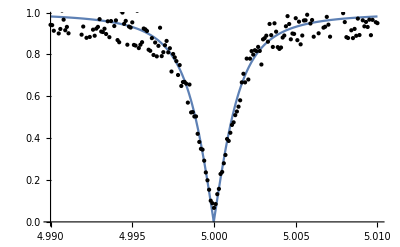

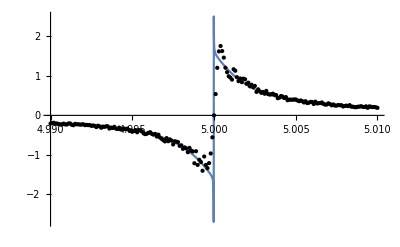

```mathematica
fitResults=FindFit[fitDataComplex,S11/.ω-> 2π x,{{κ,myκ},{ω0, myω0},{γ, myγ}},x,NormFunction->(Re[#].Re[#]+Im[#].Im[#]&)];
Plot[ Abs@S11 /. fitResults /.ω->2π x, {x,4.99,5.01}, Epilog->Point[fitDataMagnitude]]
Plot[ Arg@S11/. fitResults /.ω->2π x, {x,4.99,5.01}, Epilog->Point[fitDataPhase]]
```